```mathematica
ClearAll["Global *"]
```

```mathematica
A = {{29/9, 49/3, -49/9, 49/9}, {-20/9, -43/3, 49/9, -49/9}, {-20/9, -46/3, 49/9, -58/9}, {2, 2, 1, -1}};
B = {{1}, {-1}, {-1}, {0}};
C1 = {{-8, 24, -32, -28}};
```

```mathematica
G[s_] := (Simplify[C1.Inverse[s IdentityMatrix[4]-A].B])[[1,1]]
```

```mathematica
G[s]
```

(36 (-3+s)^2)/((3+10 s+3 s^2)^2)

```mathematica
num = Expand[Numerator[G[s]]]
```

324-216 s+36 s^2

```mathematica
den = Expand[Denominator[G[s]]]
```

9+60 s+118 s^2+60 s^3+9 s^4

```mathematica
Subscript[G, arm][s_]:= num/den
```

```mathematica
Subscript[G, arm][s]
```

(324-216 s+36 s^2)/(9+60 s+118 s^2+60 s^3+9 s^4)

```mathematica
Armas = Expand[Denominator[Subscript[G, arm][s]]Y[s]== Numerator[Subscript[G, arm][s]]Subscript[U, 12][s]]
```

9 Y[s]+60 s Y[s]+118 s^2 Y[s]+60 s^3 Y[s]+9 s^4 Y[s]==324 U_12[s]-216 s U_12[s]+36 s^2 U_12[s]

```mathematica
Armat = InverseLaplaceTransform[Armas, s,t]/.{Y[s]->LaplaceTransform[y[t],t,s], Subscript[U, 12][s]->LaplaceTransform[u[t],t,s]} /.{y[0]->0, y'[0]->0, y''[0]->0, y'''[0]->0,u[0]->0,u'[0]->0}
```

9 y[t]+60 y'[t]+118 y''[t]+60 y^(3)[t]+9 y^(4)[t]==324 u[t]-216 u'[t]+36 u''[t]

```mathematica
Subscript[x, 01]= {{-3},{2},{-3},{-2}}
```

{{-3},{2},{-3},{-2}}

```mathematica
Subscript[x, 01]//MatrixForm
```

(-3
2
-3
-2)

```mathematica
Subscript[y, 01]= (C1[[1]].Subscript[x, 01])[[1]]
```

224

```mathematica
Subscript[y, 01]' = (C1[[1]].A.Subscript[x, 01])[[1]]
```

76

```mathematica
Subscript[y, 01]'' =( C1[[1]].A.A.Subscript[x, 01])[[1]]
```

-1208/9

```mathematica
Subscript[y, 01]''' =  (C1[[1]].A.A.A.Subscript[x, 01])[[1]]
```

-34964/27

Riporto nel dominio di s

```mathematica
eqDiffL=Simplify[LaplaceTransform[Armat,t,s]/. {LaplaceTransform[y[t],t,s]->Y[s],LaplaceTransform[u[t],t,s]->Subscript[U, 12][s],u[0]->0,u'[0]->0}]
```

(3+10 s+3 s^2)^2 Y[s]==(60+118 s+60 s^2+9 s^3) y[0]+36 (-3+s)^2 U_12[s]+118 y'[0]+60 s y'[0]+9 s^2 y'[0]+60 y''[0]+9 s y''[0]+9 y^(3)[0]

```mathematica
Ydif[s_]:=Collect[Solve[eqDiffL,Y[s]][[1,1]][[2]],Subscript[U, 12][s]]/.
{y[0]->Subscript[y, 01],y'[0]->Subscript[y, 01]',y''[0]->Subscript[y, 01]'',y'''[0]->Subscript[y, 01]'''}
```

```mathematica
Ydif[s]
```

(2700+29784 s+14124 s^2+2016 s^3)/((3+10 s+3 s^2)^2)+((324-216 s+36 s^2) U_12[s])/((3+10 s+3 s^2)^2)

Trovo la rampa

```mathematica
Subscript[y, rampa][t_]:= Piecewise[{{t UnitStep[t], t>=0}, {0, t<0}}]
```

```mathematica
Subscript[y, rampa][t]
```

Piecewise[{{t UnitStep[t], t≥0}, {0, True}}]

```mathematica
Piecewise[{{t UnitStep[t], t≥0}, {0, True}}]
```

Piecewise[{{t UnitStep[t], t≥0}, {0, True}}]

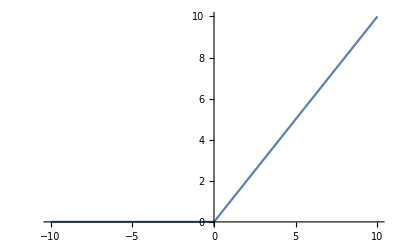

```mathematica
Plot[Subscript[y, rampa][t],{t,-10,10},PlotRange->All]
```

```mathematica
Subscript[U, rampa][s_]:=LaplaceTransform[Subscript[y, rampa][t],t,s]
```

```mathematica
Subscript[U, rampa][s]
```

1/s^2

```mathematica
Subscript[y, rampa][t_]:=Expand[InverseLaplaceTransform[((324-216 s+36 s^2) Subscript[U, 12][s])/((3+10 s+3 s^2)^2)/.
{Subscript[U, 12][s]->(1/s^2)},s,t]]
```

```mathematica
Subscript[y, rampa][t]
```

-264+(39 ⅇ^(-3 t))/16+(4185 ⅇ^(-t/3))/16+36 t+9/4 ⅇ^(-3 t) t+225/4 ⅇ^(-t/3) t

```mathematica
-264-(339 ⅇ^(-3 t))/2+(1315 ⅇ^(-t/3))/2+36 t-216 ⅇ^(-3 t) t-100/3 ⅇ^(-t/3) t
```

```mathematica
Subscript[y, transitoriar][t_]:= Subscript[y, rampa][t][[2]] +  Subscript[y, rampa][t][[3]]+ Subscript[y, rampa][t][[5]]+ Subscript[y, rampa][t][[6]]
```

```mathematica
Expand[Simplify[Subscript[y, transitoriar][t]]]
```

(39 ⅇ^(-3 t))/16+(4185 ⅇ^(-t/3))/16+9/4 ⅇ^(-3 t) t+225/4 ⅇ^(-t/3) t

```mathematica
Subscript[y, regimer][t_]:=Subscript[y, rampa][t][[1]]+Subscript[y, rampa][t][[4]]
```

```mathematica
Expand[Simplify[Subscript[y, regimer][t]]]
```

-264+36 t

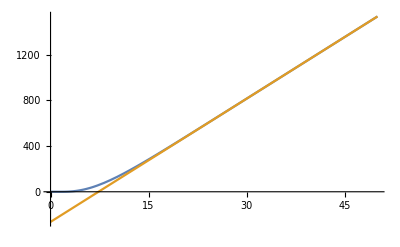

```mathematica
Plot[{-264+(39 ⅇ^(-3 t))/16+(4185 ⅇ^(-t/3))/16+36 t+9/4 ⅇ^(-3 t) t+225/4 ⅇ^(-t/3) t,-264+36 t},{t,0,50},PlotRange->All]
```

```mathematica
Subscript[y, rampa23]=Collect[Solve[eqDiffL,Y[s]][[1,1]][[2]],Subscript[U, 12][s]]/.
{Subscript[U, 12][s]->(1/s^2),y[0]->Subscript[y, 01],y'[0]->Subscript[y, 01]',y''[0]->Subscript[y, 01]'',y'''[0]->Subscript[y, 01]'''}
```

(324-216 s+36 s^2)/(s^2 (3+10 s+3 s^2)^2)+(2700+29784 s+14124 s^2+2016 s^3)/((3+10 s+3 s^2)^2)